```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica"];
Get["ctmc`"]
```

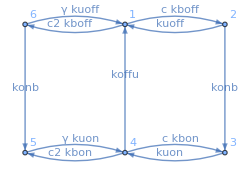

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
ClearAll[Foff1on];
offStates = {6,1,2};
onStates = {5,4,3};
Foff1on = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = Foff1on[[3]][[1]]*F31 +Foff1on[[2]][[1]]*F41 + Foff1on[[1]][[1]]*F51; (*F1off[[2]][[1]]*F41 +*)
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
ClearAll[τfun];
τfun[c_?NumericQ,c2_?NumericQ,γ_?NumericQ,kboff_?NumericQ,kbon_?NumericQ,kuoff_?NumericQ,kuon_?NumericQ,konb_?NumericQ,koffu_?NumericQ]:=Evaluate[τ];
```

```mathematica
τ/.{c2->0}
```

(c^2 kboff kbon konb γ (konb+kuoff γ)+koffu (konb+kuoff) kuon γ (konb+kuoff γ)+c kboff (konb kuon+koffu (konb+kuon)) γ (konb+kuoff γ))/(c kboff koffu konb kuon γ (konb+kuoff γ))

```mathematica
ClearAll[expr1];
ClearAll[expr2];
ClearAll[exprS1];
ClearAll[exprS12];
expr1 = FoffOn (*/.{γ->2};*)
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2];
```

(koffu kuon (c2 kboff konb^2+c2 kboff konb kuoff+c2 kboff konb s1) (kuon+s2) γ)/((c kboff konb^2+c2 kboff konb^2+c2 kboff konb kuoff+2 c kboff konb s1+2 c2 kboff konb s1+konb^2 s1+c2 kboff kuoff s1+konb kuoff s1+c kboff s1^2+c2 kboff s1^2+2 konb s1^2+kuoff s1^2+s1^3+c kboff konb kuoff γ+c kboff kuoff s1 γ+konb kuoff s1 γ+kuoff^2 s1 γ+kuoff s1^2 γ) (c2 kbon s2 (kuon+s2)+(c kbon s2+(koffu+s2) (kuon+s2)) (s2+kuon γ)))+(c kboff koffu konb kuon (konb+s1+kuoff γ) (s2+kuon γ))/((c kboff konb^2+c2 kboff konb^2+c2 kboff konb kuoff+2 c kboff konb s1+2 c2 kboff konb s1+konb^2 s1+c2 kboff kuoff s1+konb kuoff s1+c kboff s1^2+c2 kboff s1^2+2 konb s1^2+kuoff s1^2+s1^3+c kboff konb kuoff γ+c kboff kuoff s1 γ+konb kuoff s1 γ+kuoff^2 s1 γ+kuoff s1^2 γ) (c2 kbon s2 (kuon+s2)+(c kbon s2+(koffu+s2) (kuon+s2)) (s2+kuon γ)))

```mathematica
exprS12Simpl=FoffOn/.{c2->0,γ->0}//FullSimplify
```

(c kboff koffu konb kuon)/((c kboff (konb+s1)+s1 (konb+kuoff+s1)) (c kbon s2+(koffu+s2) (kuon+s2)))

```mathematica
ClearAll[Pjoint];
Pjoint=InverseLaplaceTransform[exprS12,{s1,s2},{t1,t2},Assumptions->assum];
```

```mathematica
(*Roots*)
rootLabels= {c kboff konb^2+c2 kboff konb^2+c2 kboff konb kuoff+c kboff konb kuoff γ->C1,2 c kboff konb+2 c2 kboff konb+konb^2+c2 kboff kuoff+konb kuoff+c kboff kuoff γ+konb kuoff γ+kuoff^2 γ->C2,
c kboff+c2 kboff+2 konb+kuoff+kuoff γ->C3,
koffu kuon^2 γ->C4,
c2 kbon kuon+koffu kuon+c kbon kuon γ+koffu kuon γ+kuon^2 γ->C5,
c kbon+c2 kbon+koffu+kuon+kuon γ->C6,
Root[C1+C2#1+C3 #1^2+#1^3&,1]->A1,
Root[C1+C2#1+C3 #1^2+#1^3&,2]->A2,
Root[C1+C2#1+C3 #1^2+#1^3&,3]->A3,
Root[C4+C5#1+C6 #1^2+#1^3&,1]->B1,
Root[C4+C5#1+C6 #1^2+#1^3&,2]->B2,
Root[C4+C5#1+C6 #1^2+#1^3&,3]->B3};
```

```mathematica
Pjoint
```

```mathematica
integrand =D[Pjoint,{c,1}]^2/Pjoint;(*-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2*)
```

```mathematica
integrandSimpl=integrand//.rootLabels;
```

```mathematica
integrandC=Compile[{{A1,_Real},{A2,_Real},{A3,_Real},{B1,_Real},{B2,_Real},{B3,_Real},{c,_Real},{c2,_Real},{γ,_Real},{C1,_Real},{C2,_Real},{C3,_Real},{C4,_Real},{C5,_Real},{C6,_Real},{kboff,_Real},{kbon,_Real},{kuoff,_Real},{kuon,_Real},{konb,_Real},{koffu,_Real},{t1,_Real},{t2,_Real}},
Evaluate[integrandSimpl],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

CompiledFunction[{A1, A2, A3, B1, B2, B3, c, c2, γ, C1, C2, C3, C4, C5, C6, kboff, kbon, kuoff, kuon, konb, koffu, t1, t2}, Block[{Compile`$1115, Compile`$1121, Compile`$1128, Compile`$1129, Compile`$1131, Compile`$1132, Compile`$1142, Compile`$1143, Compile`$1144, <<12>>3, «533», Compile`$3396, Compile`$3445, Compile`$3446, Compile`$3495, Compile`$3544}, «1»], -CompiledCode-]

```mathematica
integrandC[0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.1,2.2,2.3,2.4,2.5]
```

7.41209×10^6

```mathematica
ClearAll[integrandNum];
integrandNum[A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,c_?NumericQ,c2_?NumericQ,γ_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,C4_?NumericQ,C5_?NumericQ,C6_?NumericQ,kboff_?NumericQ,kbon_?NumericQ,kuoff_?NumericQ,kuon_?NumericQ,konb_?NumericQ,koffu_?NumericQ,t1_?NumericQ,t2_?NumericQ]:=integrandC[N[A1],N[A2],N[A3],N[B1],N[B2],N[B3],N[c],N[c2],N[γ],N[C1],N[C2],N[C3],N[C4],N[C5],N[C6],N[kboff],N[kbon],N[kuoff],N[kuon],N[konb],N[koffu],N[t1],N[t2]];
```

```mathematica
integrandNum[0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.1,2.2,2.3,2.4,2.5]
```

7.41209×10^6

```mathematica
ClearAll[FisherFast];
ClearAll[FisherSafe];

(*kboff2,kuoff,kuon,c*kbon2,kon1b,c*kboff,c*kbon,kuoff2,kon2b,kuon2,koffu*)
FisherFast[c_?NumericQ,c2_?NumericQ,γ_?NumericQ,kboff_?NumericQ,kbon_?NumericQ,kuoff_?NumericQ,kuon_?NumericQ,konb_?NumericQ,koffu_?NumericQ]:=Module[{τeval,integral,A1,A2,A3,B1,B2,B3,C1,C2,C3,C4,C5,C6},
τeval=τfun[c,c2,γ,kboff,kbon,kuoff,kuon,konb,koffu];
C1=c kboff konb^2+c2 kboff konb^2+c2 kboff konb kuoff+c kboff konb kuoff γ;C2=2 c kboff konb+2 c2 kboff konb+konb^2+c2 kboff kuoff+konb kuoff+c kboff kuoff γ+konb kuoff γ+kuoff^2 γ;
C3=c kboff+c2 kboff+2 konb+kuoff+kuoff γ;
C4=koffu kuon^2 γ;
C5=c2 kbon kuon+koffu kuon+c kbon kuon γ+koffu kuon γ+kuon^2 γ;
C6=c kbon+c2 kbon+koffu+kuon+kuon γ;
A1=Root[C1+C2#1+C3 #1^2+#1^3&,1];
A2=Root[C1+C2#1+C3 #1^2+#1^3&,2];
A3=Root[C1+C2#1+C3 #1^2+#1^3&,3];
B1=Root[C4+C5#1+C6 #1^2+#1^3&,1];
B2=Root[C4+C5#1+C6 #1^2+#1^3&,2];
B3=Root[C4+C5#1+C6 #1^2+#1^3&,3];
integral=NIntegrate[integrandNum[A1,A2,A3,B1,B2,B3,c,c2,γ,C1,C2,C3,C4,C5,C6,kboff,kbon,kuoff,kuon,konb,koffu,t1,t2],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential"},
PrecisionGoal->5,
MinRecursion->3,
MaxRecursion->10];
integral*c^2/τeval];

FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherFast[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
],{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
];
```

```mathematica
kmin =0.0001;
kmax = 5.;
kdl=0.0888;
c0val=100;
ω=0;
c2val=ω*c0val;
γval=1;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0val]];
FisherSafe[c0val,c2val,γval,kbofflim,kmin,kmin,kmax,kmax,kmax]
```

0.807909

```mathematica
kbofflim
```

0.05

```mathematica
kmin =0.001;
kmax = 5.;
kdl=0.0888;
c0=40.;
ω=0.;
c2=ω*c0;
γ=1.;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
FisherSafe[c0,c2,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.806061

```mathematica
FisherSafeLog[c0_,c2_,γ_,lnkboff,lnkonb,lnkuon,lnkbon,lnkoffu,lnkuoff,lnkonu]:=FisherSafe[c0,c2,γ,Exp[lnkboff],Exp[lnkonb],Exp[lnkuon],Exp[lnkbon],Exp[lnkoffu],Exp[lnkuoff],Exp[lnkonu]];
```

```mathematica
ClearAll[TestFun];
TestFun[c0_,kboff_,kbon_,kuoff_,konu_ ]:=Module[{},
Pause[1];
-(kboff-kdl)^2-(kbon-kdl)^2-(kuoff-3)^2-(konu-4)^2+c0];
```

```mathematica
cvals=10^Range[-1.,2.,3/27];
```

```mathematica
ω=0.1;
γ=1.;
kmin =0.0001;
kmax = 5;
kdl=0.0888;

(*Save the data*)
dir = ".julia/dev/LLROpt/mathematica-nbs";
datadir = FileNameJoin[dir,"data"];
plotdir = FileNameJoin[dir,"plots"];
date = "20250504";
```

```mathematica
(*c0,c2,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu*)
evals=0;
ParallelDo[
results=Reap[
Catch[
TimeConstrained[
NMaximize[
{TestFun[cvals[[i]],kboff,kbon,kuoff,konu],
kmin<=kboff<=kdl,
kmin<=kbon<=kdl,
kmin<=kuoff<=kmax,
kmin<=konu<=kmax},
{kboff,kbon,kuoff,konu},
Method->"NelderMead",
PrecisionGoal->6,AccuracyGoal->6,MaxIterations->10
],2,Throw["timeout",$tag]
],$tag
]
];
Save[FileNameJoin[{$HomeDirectory},datadir, date, "test-output-pid"<>ToString[i]<>".wl"],results]
,{i,1,28}
]
```

```mathematica
ClearAll[f,timedRun]

(*a toy integrand that Sows something each time it is called*)
f[x_]:=(Sow[{x}];Pause[1];1/(1+x^2));

(*-----------------------------------------------------------*)
(*timedRun[...] runs expr for at most t seconds.*)
(*It returns {result,listOfSows} if finished,*)
(*or {"timeout",listOfSows} if it hit the limit.*)
(*-----------------------------------------------------------*)
timedRun[expr_,t_]:=Reap@Catch[
TimeConstrained[expr,(*the job*)
t,
Throw["timeout",$tag]                          (*on timeout*)
],$tag                                              (*Catch label*)
];
```

```mathematica
timedRun[NIntegrate[Evaluate@f[x],{x,0,∞}],(*integrand Sows each call*)
0.0001                                   (*time limit in seconds*)
]
```

{1.5708,{}}

```mathematica
f[i_]:=results[[i]];
```

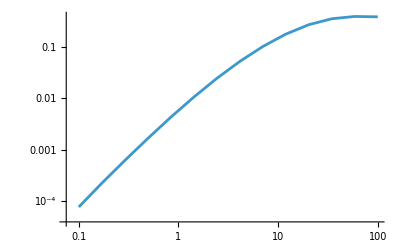

```mathematica
ListLinePlot[Table[{cvals[[i]],results[[i]]},{i,1,14}],ScalingFunctions->{"Log","Log"}]
```

```mathematica
i=14;(*c0,c2,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu*)
kdl=5*0.503427/100;
FisherSafe[cvals[[i]],0*cvals[[i]],γ,kdl,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.804384

```mathematica
(*Joint PDF of OFF durations*)
ClearAll[Poff];
ClearAll[d2LogPoff];
ClearAll[integrandOff];

Foff=Foff1on[[3]][[1]] +Foff1on[[2]][[1]] + Foff1on[[1]][[1]];
expr1off = Foff /.{γ->5};
expr2off=Factor[expr1off,Modulus->0];
exprS1off=Apart[expr2off,s1]
```

(c kboff konb^2+c2 kboff konb^2+konb^2 konu+5 c kboff konb kuoff+c2 kboff konb kuoff+6 konb konu kuoff+5 konu kuoff^2+c kboff konb s1+c2 kboff konb s1+2 konb konu s1+6 konu kuoff s1+konu s1^2)/(c kboff konb^2+c2 kboff konb^2+konb^2 konu+5 c kboff konb kuoff+c2 kboff konb kuoff+6 konb konu kuoff+5 konu kuoff^2+2 c kboff konb s1+2 c2 kboff konb s1+konb^2 s1+2 konb konu s1+5 c kboff kuoff s1+c2 kboff kuoff s1+6 konb kuoff s1+6 konu kuoff s1+5 kuoff^2 s1+c kboff s1^2+c2 kboff s1^2+2 konb s1^2+konu s1^2+6 kuoff s1^2+s1^3)

```mathematica
Poff=InverseLaplaceTransform[exprS1off,{s1},{t1},Assumptions->assum]
```

```mathematica
(*A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konb konu+konu kuoff)-B/2==-(c kboff)/2-(c2 kboff)/2-konb/2-konu/2-kuoff/2*)
Simplify[Poff,{A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konb konu+konu kuoff),-B/2==-(c kboff)/2-(c2 kboff)/2-konb/2-konu/2-kuoff/2}]
```

$Aborted

Poff

```mathematica
d2LogPoff =D[Log[Poff],{c,2}];
integrandOff = Poff *d2LogPoff;
```

```mathematica
integrandOff/.{t1->0.1,c->1., c2->1., kboff->2., kbon->2.,konb->3.,konu->1.,kuon->1.,kuoff->2.,kuon->1.}
```

-0.0695138

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*New definition of specificity*)

(*Edge lists and weights*)
edges={{1,2},{2,1},{1,6},{6,1},{7,3},{3,7},
	    {4,5},{5,4},{6,5},{7,1},{2,3},{4,1},{7,5},{4,3}};
weights={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,koffu,c2*kbon,c*kbon};
nstates = 7;
nedges = Length[edges];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
HomeDir="/home/tohme/.julia/dev/LLROpt/";
circuitData=Import[HomeDir<>"spec/circuits.json","RawJSON"];

(*circuitId="1bs_decoy_no_konu_new";*)
circuitId="1bs_decoy_no_konu_new";
edges=circuitData[circuitId]["edges"];
weights=ToExpression[circuitData[circuitId]["weight_labels"]];
nstates=circuitData[circuitId]["nstates"];
vertexPartition=circuitData[circuitId]["vertex_partition"];
nedges=Length[edges];
offInd=circuitData[circuitId]["off_indicator"];
onInd=1-offInd;

assum=c>=0&&kboff>0&&kboff2>0&&kuon>0&&kuon2>0&&kbon>0&&kbon2>0&&kon1b>0&&kuoff>0&&kuoff2>0&&kon2b>0&&koffu>0;
(*Plot the circuit*)
edgeList=Table[edges[[i,1]]->edges[[i,2]],{i,1,nedges}];
g=Graph[edges,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights)[[i]],0.55],{i,1,nedges}],ImageSize->250,GraphLayout->{"MultipartiteEmbedding","VertexPartition"->vertexPartition}];
```

```mathematica
coords=GraphEmbedding[g];
coords[[4]][[1]]=coords[[4]][[1]] - 0.1;
coords[[7]][[1]]=coords[[7]][[1]] + 0.1;
coords[[7]][[2]]=coords[[7]][[2]] - 0.1;
coords[[4]][[2]]=coords[[4]][[2]] + 0.1;
coords[[1]][[2]]=coords[[1]][[2]] - 0.1;
```

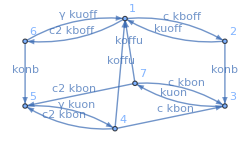

```mathematica
Graph[edges,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights)[[i]],0.55],{i,1,nedges}],ImageSize->250,VertexCoordinates->coords]
```

```mathematica
Q=RateMatrix[edges,weights,nstates];
ss=SteadyStateProbabilities[Q];
MatrixForm[Q]
```

(-c kboff-c2 kboff | c kboff | 0 | 0 | 0 | c2 kboff | 0
kuoff | -konb-kuoff | konb | 0 | 0 | 0 | 0
0 | 0 | -kuon | 0 | 0 | 0 | kuon
koffu | 0 | c kbon | -c kbon-c2 kbon-koffu | c2 kbon | 0 | 0
0 | 0 | 0 | kuon γ | -kuon γ | 0 | 0
kuoff γ | 0 | 0 | 0 | konb | -konb-kuoff γ | 0
koffu | 0 | c kbon | 0 | c2 kbon | 0 | -c kbon-c2 kbon-koffu)

```mathematica
circuitId2="1bs_decoy_no_konu";
edges2=circuitData[circuitId2]["edges"];
weights2=ToExpression[circuitData[circuitId2]["weight_labels"]];
nstates2=circuitData[circuitId2]["nstates"];
vertexPartition2=circuitData[circuitId2]["vertex_partition"];
nedges2=Length[edges2];
offInd2=circuitData[circuitId2]["off_indicator"];
onInd2=1-offInd2;

edgeList2=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList2[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250,VertexCoordinates->coords]
```

```mathematica
Qold=RateMatrix[edges2,weights2,nstates2];
ssold=SteadyStateProbabilities[Qold];
MatrixForm[Qold]
```

(-c kboff-c2 kboff | c kboff | 0 | 0 | 0 | c2 kboff
kuoff | -konb-kuoff | konb | 0 | 0 | 0
0 | 0 | -kuon | kuon | 0 | 0
koffu | 0 | c kbon | -c kbon-c2 kbon-koffu | c2 kbon | 0
0 | 0 | 0 | kuon γ | -kuon γ | 0
kuoff γ | 0 | 0 | 0 | konb | -konb-kuoff γ)

```mathematica
Simplify[ss[[4]]+ss[[7]]]
```

(kboff konb kuon γ (c2 (konb+kuoff)+c (konb+kuoff γ)))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c kboff ((konb kuon+koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+koffu kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ))))

```mathematica
Simplify[ssold[[4]]]
```

(kboff konb kuon γ (c2 (konb+kuoff)+c (konb+kuoff γ)))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c kboff ((konb kuon+koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+koffu kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ))))